# COVID-2019

## Retrieving data

```mathematica
ds=ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"];
ds[1;;2](*Printing to many will result in crash of Mathematica editor*)
```

Dataset[<>]

## Some basic data ploting and data manipulation

## Worldwide data

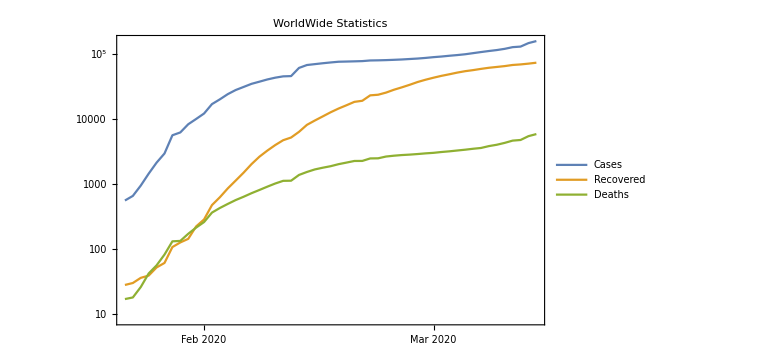

```mathematica
DateListLogPlot[
{
ds[Total, "ConfirmedCases"],
ds[Total, "RecoveredCases"],
ds[Total, "Deaths"]
}, 
PlotLegends->{"Cases","Recovered", "Deaths"},
PlotLabel->"WorldWide Statistics",
ImageSize->Large
]
```

```mathematica
24 3600 7(*number of seconds in weekend*)
```

604800

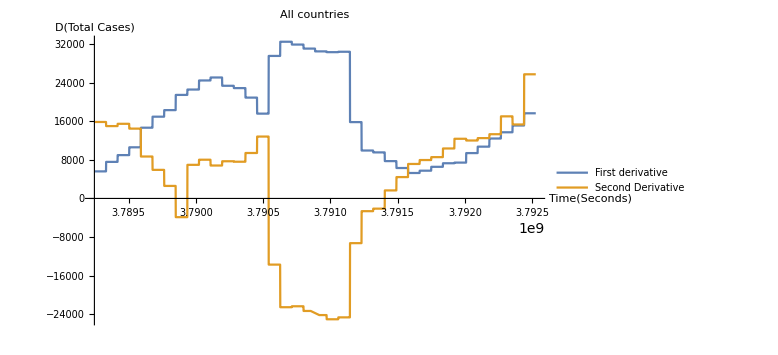

```mathematica
func = ds[Total, "ConfirmedCases"]["PathFunction"];
Plot[
{
func[x]-func[x-604800],
-2*func[x]+func[x-604800]+func[x+604800]
},
{x,3788640000+604800,3793132800-604800},
PlotRange->All,
AxesOrigin->{3788640000+604800, 0},
PlotLabel->"All countries",
PlotLegends->{"First derivative", "Second Derivative"},
AxesLabel->{"Time(Seconds)", "D(Total Cases)"},
ImageSize->Large
]
```

### Grouping by countries

```mathematica
dsGrouped=ds[GroupBy["Country"]];
```

### Example of data access

```mathematica
uaCases=dsGrouped[Entity["Country","Ukraine"],1,"ConfirmedCases"]
uaDeaths=dsGrouped[Entity["Country","Ukraine"],1,"Deaths"]
```

TimeSeries[…]

TimeSeries[…]

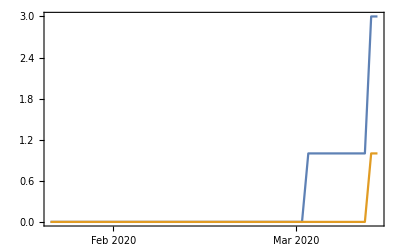

```mathematica
DateListPlot[{uaCases,uaDeaths}]
```

```mathematica
worldwideCountryList = DeleteMissing[Normal[Keys[dsGrouped]]]
```

{China,Italy,Iran,South Korea,Spain,Germany,France,Switzerland,United Kingdom,Norway,Sweden,Netherlands,Denmark,Japan,Belgium,Austria,United States,Qatar,Malaysia,Greece,Finland,Singapore,Bahrain,Israel,Czech Republic,Slovenia,Portugal,Iceland,Brazil,Hong Kong,Ireland,Romania,Estonia,Australia,Philippines,Iraq,Egypt,Kuwait,Saudi Arabia,Poland,India,Indonesia,Lebanon,United Arab Emirates,Thailand,San Marino,Canada,Chile,Russia,Vietnam,Taiwan,Luxembourg,Serbia,Slovakia,Bulgaria,Brunei,South Africa,Peru,Croatia,Albania,Algeria,Panama,Argentina,Pakistan,Hungary,Georgia,Ecuador,Belarus,Mexico,Latvia,Cyprus,Costa Rica,Colombia,Oman,Tunisia,Malta,Bosnia and Herzegovina,Armenia,Morocco,Azerbaijan,North Macedonia,Moldova,Dominican Republic,Afghanistan,Sri Lanka,Senegal,Maldives,Macau,Bolivia,Martinique,Faroe Islands,Lithuania,Jamaica,Cambodia,Réunion,Paraguay,New Zealand,Kazakhstan,Turkey,French Guiana,Uruguay,Liechtenstein,Cuba,Ukraine,Puerto Rico,Ghana,French Polynesia,Bangladesh,Venezuela,Trinidad and Tobago,Seychelles,Saint Martin,Nigeria,Namibia,Monaco,Jersey,Honduras,Democratic Republic of the Congo,Cameroon,Burkina Faso,Aruba,Vatican City,United States Virgin Islands,Togo,Eswatini,Suriname,Sudan,Saint Vincent and the Grenadines,Saint Lucia,Saint Barthelemy,Rwanda,Nepal,Mongolia,Mauritania,Kenya,Jordan,Ivory Coast,Guyana,Guinea,Guernsey,Guatemala,Guadeloupe,Gibraltar,Gabon,Ethiopia,Curacao,Cayman Islands,Bhutan,Antigua and Barbuda,Andorra}

## Europe

```mathematica
europeCountryList=Intersection[CountryData["Europe"],worldwideCountryList]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Italy,Jersey,Latvia,Liechtenstein,Lithuania,Luxembourg,North Macedonia,Malta,Moldova,Monaco,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

```mathematica
dsEurope = dsGrouped[europeCountryList];
```

```mathematica
dsEurope[Total, 1,"ConfirmedCases"]
```

TimeSeries[…]

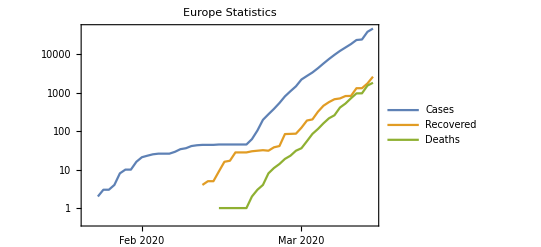

```mathematica
DateListLogPlot[
{
dsEurope[Total, 1,"ConfirmedCases"],
dsEurope[Total, 1,"RecoveredCases"],
dsEurope[Total, 1,"Deaths"]
}, 
PlotLegends->{"Cases","Recovered", "Deaths"},
PlotLabel->"Europe Statistics"
]
```

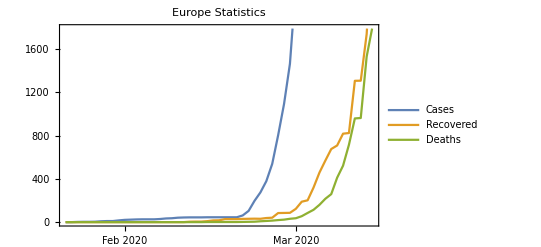

```mathematica
DateListPlot[
{
dsEurope[Total, 1,"ConfirmedCases"],
dsEurope[Total, 1,"RecoveredCases"],
dsEurope[Total, 1,"Deaths"]
}, 
PlotLegends->{"Cases","Recovered", "Deaths"},
PlotLabel->"Europe Statistics"
]
```

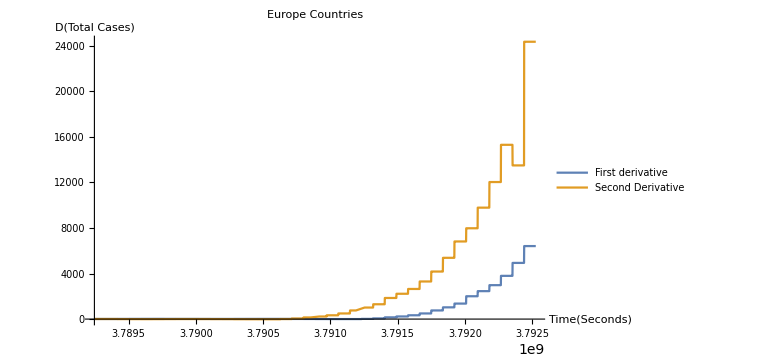

```mathematica
func = dsEurope[Total, 1,"ConfirmedCases"]["PathFunction"];
Plot[
{
func[x]-func[x-604800],
-2*func[x]+func[x-604800]+func[x+604800]
},
{x,3788640000+604800,3793132800-604800},
PlotRange->All,
AxesOrigin->{3788640000+604800, 0},
PlotLabel->"Europe Countries",
PlotLegends->{"First derivative", "Second Derivative"},
AxesLabel->{"Time(Seconds)", "D(Total Cases)"},
ImageSize->Large
]
```

## Logistic Curve

```mathematica
func = dsEurope[Total, 1,"ConfirmedCases"]["PathFunction"];
```

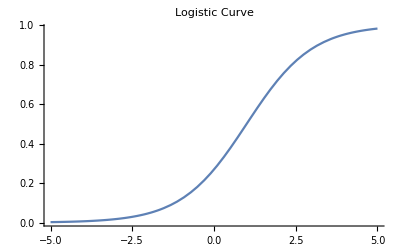

```mathematica
Plot[1/(1+Exp[-1(t-1)]),{t,-5,5},PlotRange->All, PlotLabel->"Logistic Curve"]
```

```mathematica
data = Table[{t, func[t]},{t,3788640000,3793132800, 24*360*7}];
```

```mathematica
Manipulate[
Show[
ListLogPlot[data, 
Joined->True,
PlotRange->{{3788640000, 3799132800},{0,80000}},
AxesLabel->{"Time(seconds)", "Confirmed Cases"},
PlotLabel->"Fitting Logistic Curve"
],
LogPlot[
L/(1+Exp[-k(t-t0)]),
{t,3788640000,3883132800}
]//Quiet
],
{{L ,5000}, 0, 100000},
{{k,5.2*^-6}, 0, 0.0001},
{{t0,3.79226*^9},3790640000,3793132800}
]
```

## Fitting second derivative

```mathematica
D[L/(1+Exp[-k(t-t0)]),{t,2}]
```

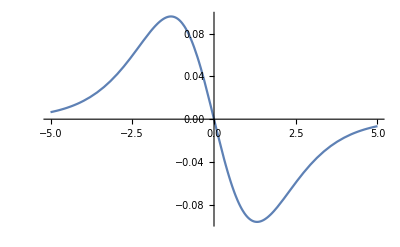

```mathematica
Plot[((2 ⅇ^(-2 k (t-t0)) k^2)/((1+ⅇ^(-k (t-t0)))^3)-(ⅇ^(-k (t-t0)) k^2)/((1+ⅇ^(-k (t-t0)))^2)) /.{L->1, k->1, t0->0},{t,-5,5}]
```

## Animation

```mathematica
imagesCasesBubble = Table[
GeoBubbleChart[
#->dsGrouped[#,1,"ConfirmedCases"][t]&/@worldwideCountryList,
ColorFunction->ColorData["Rainbow"],
ImageSize->Large
],
{t,
DateRange[
CurrentDate[{2020, 2, 1},"Day"],
Today,
0.5]
}
]//Quiet;
Export[NotebookDirectory[]<>"epidemy_bubble.gif",imagesCasesBubble];
```

```mathematica
imagesCasesBubbleEurope = Table[
GeoBubbleChart[
#->dsGrouped[#,1,"ConfirmedCases"][t]&/@europeCountryList,
ColorFunction->ColorData["Rainbow"],
ImageSize->Large
],
{t,
DateRange[
CurrentDate[{2020, 2, 1},"Day"],
Today,
0.5]
}
]//Quiet;
Export[NotebookDirectory[]<>"epidemy_bubble_europe.gif",imagesCasesBubbleEurope];
```

```mathematica
First[imagesCasesBubble]
First[imagesCasesBubbleEurope]
```

-Graphics-

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"epidemy_region.gif",imagesCasesRegion];
```

### Useful link: https://blog.wolfram.com/2014/11/04/modeling-a-pandemic-like-ebola-with-the-wolfram-language/